# Example

## Setup

Set working directory

```mathematica
SetDirectory["/Users/nicoloceneda/Dropbox/Bhamra-Ceneda/theory/macroeconomics/PS1/code"];
```

## Question 2

Maximum safe to spend

```mathematica
maxC[μ_,T_]:=(μ*w0)/(1-ⅇ^(-μ*T))
```

Parameters

```mathematica
w0=1;
```

Plot household maximum safe to spend and wealth

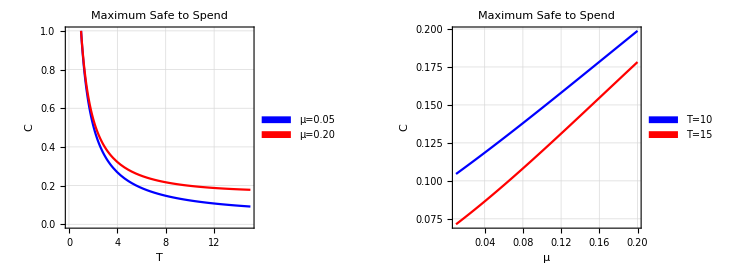

```mathematica
maxSafeSpend1= Plot[{maxC[0.05,T],maxC[0.20,T]},{T,0.01,15},
PlotStyle->{Blue,Red},
PlotLabel->"Maximum Safe to Spend",
PlotLegends->Placed[SwatchLegend[{"μ=0.05","μ=0.20"}],{0.87,0.88}],
FrameLabel->{"T","C"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{0,1}}];
maxSafeSpend2= Plot[{maxC[μ,10],maxC[μ,15]},{μ,0.01,0.20},
PlotStyle->{Blue,Red},
PlotLabel->"Maximum Safe to Spend",
PlotLegends->Placed[SwatchLegend[{"T=10","T=15"}],{0.13,0.88}],
FrameLabel->{"μ","C"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0.01,0.20},{Min[maxC[0.01,10],maxC[0.01,15]],Max[maxC[0.20,10],maxC[0.20,15]]}}];
maxSafeSpend=GraphicsGrid[{{maxSafeSpend1,maxSafeSpend2}},ImageSize->{750,270}]
Export["images/max-safe-spend.jpeg",maxSafeSpend];
```

```mathematica
Max[Max[maxC[0.01,10],maxC[0.01,15]]]
```

0.104537